RR>1, proceed as normal

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

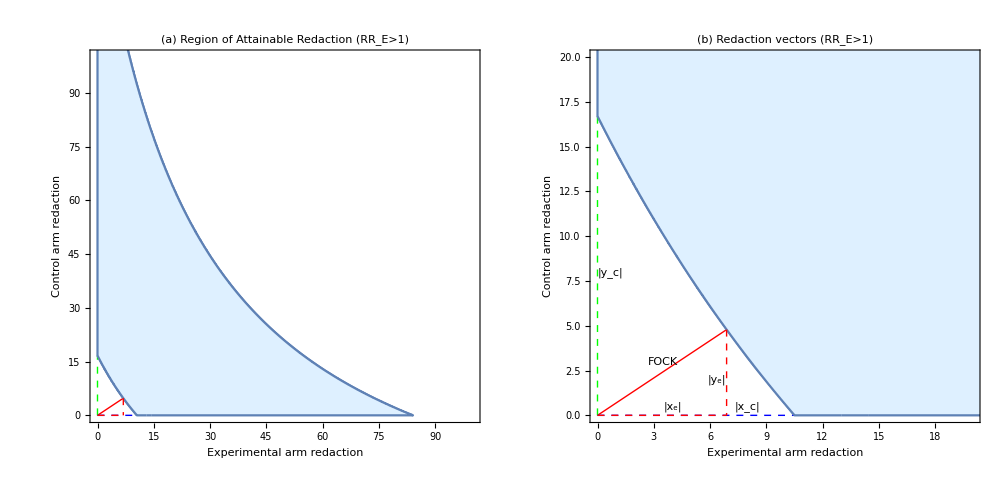

```mathematica
ClearAll["Global`*"]

(*ROAR analysis - Mathematica visualisation*)

v =3.814;
a = 70;
b = 30;
c = 50;
d = 50;
n = a + b +c +d;

eqe = (n+x + y)((a*d - (b+x)(c+y))^2) -v(a+b+x)(c+d+y)(a+c+y)(b +d + x); 
lineout1 = ContourPlot[eqe==  0,{x,0,150},{y,0,150}];

ratiocheck = (a/(a+b))/(c/(c+d));

If[ratiocheck>1,
(Print["RR>1, proceed as normal"];
coeffx3y2 = 1;
coeffx3y = 2*c;
coeffx3 =c^2;
coeffx2y3 =1;
coeffx2y2 =n + 2(b+c) - v;
coeffx2y =4 *b* c+c^2-2* a* d+2* c* n-(a+2 c+d) v;
coeffx2 =c (2 *b* c-2* a* d+c* n)-(a+c) (c+d) v;
coeffxy3 =2*b;
coeffxy2 =b^2+4 *b* c-2* a* d+2* b* n-(a+2 b+d) v;
coeffxy =2 (b+c) (b *c-a* d)+4* b* c* n-2* a* d* n-(a+2 b+d) (a+2 c+d) v;
coeffx =(b*c-a*d) (b*c-a*d+2*c*n)-(a+c) (a+2 b+d) (c+d) v;
coeffy3 =b^2; 
coeffy2 =b (-2*a*d+b (2*c+n))-(a+b) (b+d) v;
coeffy =(b*c-a*d) (-a*d+b (c+2 n))-(a+b) (b+d) (a+2 c+d) v;
coeffc = (b c-a d)^2 n-(a+b) (a+c) (b+d) (c+d) v;

gfull = coeffx3y2*(x^3*y^2) + coeffx3y*(x^3*y) + coeffx3*(x^3) + coeffx2y3*(x^2*y^3) + coeffx2y2*(x^2*y^2) + coeffx2y*(x^2*y) + coeffx2*(x^2) + coeffxy3*(x*y^3) + coeffxy2*(x*y^2)+ coeffxy*(x*y) + coeffx*(x) + coeffy3(y^3) + coeffy2(y^2) + coeffy*(y) + coeffc;

gf[x_,y_]:= coeffx3y2*(x^3*y^2) + coeffx3y*(x^3*y) + coeffx3*(x^3) + coeffx2y3*(x^2*y^3) + coeffx2y2*(x^2*y^2) + coeffx2y*(x^2*y) + coeffx2*(x^2) + coeffxy3*(x*y^3) + coeffxy2*(x*y^2)+ coeffxy*(x*y) + coeffx*(x) + coeffy3(y^3) + coeffy2(y^2) + coeffy*(y) + coeffc;  

disfun = Sqrt[x^2 + y^2];

dgdx = D[gfull,x];
dgdy = D[gfull,y];
dDdx = D[disfun,x];
dDdy = D[disfun,y];
eqsimp = Expand[y*(dgdx) - x*(dgdy)];

sollist = Assuming[x ≥ 0 && y≥ 0  && a > 0 && b > 0 && c > 0 && d > 0 && n > 0 && v > 0, Solve[gfull==0&&eqsimp ==0,{x,y}]];

realroots=Cases[sollist,{_->_Real,_->_Real}];
solxy = {x,y}/.realroots;
possols=Select[solxy,#[[1]]>0&&#[[2]]>0&];
sofs=Sqrt[Total[#^2]]&/@possols;
mind = Min[sofs];
minv = Position[sofs,mind];
mval = minv[[1]][[1]];



xe = possols[[mval]][[1]];
ye = possols[[mval]][[2]];

rp:={xe,ye};
pz := {0,0}; 
rx := {xe,0};
ry := {0,ye};
lp=Graphics[{Thick,Red, Line[{pz,rp}]}];
lpx=Graphics[{Thin,Dashed,Red, Line[{rp,rx}]}];
lpy=Graphics[{Thin,Dashed,Red, Line[{pz,rx}]}];

(*now min vectors x y*)
gyfull = gfull/.x-> 0;
gxfull = gfull/.y-> 0;

solxc = Assuming[x ≥ 0 , Solve[gxfull==0,x]];
solyc = Assuming[y ≥ 0 , Solve[gyfull==0,y]];
solx = x/.solxc;
xv =Select[solx,#>0 &];
soly = y/.solyc;
yv = Select[soly,#>0 &];
xc = Min[xv];
yc = Min[yv];
xcv:={xc,0};
ycv:={0,yc};
lyv=Graphics[{Thick,Dashed,Green, Line[{pz,ycv}]}];
lyx=Graphics[{Thick,Dashed,Blue, Line[{pz,xcv}]}];

aout = RegionPlot[gfull≤ 0,{x,0,110},{y,0,110}, MaxRecursion->10, PlotStyle->LightBlue];
angche = ArcTan[ye/xe];
gfoc =Graphics[Rotate[Style[Text["FOCK",{3.5,3}],15],angche]];
g1 = Graphics[Style[Text["|y_c|",{0.7,8}],15]];
g2 = Graphics[Style[Text["|x_c|",{8,0.5}],15]];
g3 = Graphics[Style[Text["|x_e|",{4,0.5}],15]];
g4 = Graphics[Style[Text["|y_e|",{6.35,2}],15]];


figb = Show[lineout1,lp,aout,gfoc,lyv,lyx,lpx,lpy,g1,g2,g3,g4,PlotRange->{{0,20},{0,20}},FrameLabel->{"Experimental arm redaction","Control arm redaction"},PlotLabel-> "(b) Redaction vectors (RR_E>1)",LabelStyle->{Bold,FontSize->14},ImageSize->500];
figa = Show[lineout1,lp,aout,lyv,lyx,lpx,lpy,PlotRange->{{0,100},{0,100}},FrameLabel->{"Experimental arm redaction","Control arm redaction"},PlotLabel-> "(a) Region of Attainable Redaction (RR_E>1)",LabelStyle->{Bold,FontSize->14},ImageSize->500];

outerlimits = GraphicsRow[{figa,figb},Spacings->0,ImageSize->1000]
) (*This is block A*)
,
(Print["flipz"];
coeffx3y2 = 1;
coeffx3y = 2*d;
coeffx3 =d^2;
coeffx2y3 =1;
coeffx2y2 =n + 2(a+d) - v;
coeffx2y =-2* b* c+d (4 *a+d+2* n)-(b+c+2 d) v;
coeffx2 =d (-2 *b* c+d (2 *a+n))-(b+d) (c+d) v;
coeffxy3 =2*a;
coeffxy2 =-2 *b* c+a (a+4 *d+2 *n)-(2 *a+b+c) v;
coeffxy =2 (a+d) (-b* c+a* d)-2* b* c* n+4* a* d* n-(2 *a+b+c) (b+c+2 *d) v;
coeffx =(b *c-a* d) (b* c-d (a+2 *n))-(2 *a+b+c) (b+d) (c+d) v;
coeffy3 =a^2; 
coeffy2 =a (-2* b* c+a (2 *d+n))-(a+b) (a+c) v;
coeffy =(b* c-a *d) (b* c-a (d+2 *n))-(a+b) (a+c) (b+c+2 *d) v;
coeffc = (b c-a d)^2 n-(a+b) (a+c) (b+d) (c+d) v;

gfull = coeffx3y2*(x^3*y^2) + coeffx3y*(x^3*y) + coeffx3*(x^3) + coeffx2y3*(x^2*y^3) + coeffx2y2*(x^2*y^2) + coeffx2y*(x^2*y) + coeffx2*(x^2) + coeffxy3*(x*y^3) + coeffxy2*(x*y^2)+ coeffxy*(x*y) + coeffx*(x) + coeffy3(y^3) + coeffy2(y^2) + coeffy*(y) + coeffc;

gf[x_,y_]:= coeffx3y2*(x^3*y^2) + coeffx3y*(x^3*y) + coeffx3*(x^3) + coeffx2y3*(x^2*y^3) + coeffx2y2*(x^2*y^2) + coeffx2y*(x^2*y) + coeffx2*(x^2) + coeffxy3*(x*y^3) + coeffxy2*(x*y^2)+ coeffxy*(x*y) + coeffx*(x) + coeffy3(y^3) + coeffy2(y^2) + coeffy*(y) + coeffc;  

disfun = Sqrt[x^2 + y^2];

dgdx = D[gfull,x];
dgdy = D[gfull,y];
dDdx = D[disfun,x];
dDdy = D[disfun,y];
eqsimp = Expand[y*(dgdx) - x*(dgdy)];

sollist = Assuming[x ≥ 0 && y≥ 0  && a > 0 && b > 0 && c > 0 && d > 0 && n > 0 && v > 0, Solve[gfull==0&&eqsimp ==0,{x,y}]];

realroots=Cases[sollist,{_->_Real,_->_Real}];
solxy = {x,y}/.realroots;
possols=Select[solxy,#[[1]]>0&&#[[2]]>0&];
sofs=Sqrt[Total[#^2]]&/@possols;
mind = Min[sofs];
minv = Position[sofs,mind];
mval = minv[[1]][[1]];



xe = possols[[mval]][[1]];
ye = possols[[mval]][[2]];

rp:={xe,ye};
pz := {0,0}; 
rx := {xe,0};
ry := {0,ye};
lp=Graphics[{Thick,Red, Line[{pz,rp}]}];
lpx=Graphics[{Thin,Dashed,Red, Line[{rp,rx}]}];
lpy=Graphics[{Thin,Dashed,Red, Line[{pz,rx}]}];

(*now min vectors x y*)
gyfull = gfull/.x-> 0;
gxfull = gfull/.y-> 0;

solxc = Assuming[x ≥ 0 , Solve[gxfull==0,x]];
solyc = Assuming[y ≥ 0 , Solve[gyfull==0,y]];
solx = x/.solxc;
xv =Select[solx,#>0 &];
soly = y/.solyc;
yv = Select[soly,#>0 &];
xc = Min[xv];
yc = Min[yv];
xcv:={xc,0};
ycv:={0,yc};
lyv=Graphics[{Thick,Dashed,Green, Line[{pz,ycv}]}];
lyx=Graphics[{Thick,Dashed,Blue, Line[{pz,xcv}]}];

aout = RegionPlot[gfull≤ 0,{x,0,150},{y,0,150}, MaxRecursion->10, PlotStyle->LightBlue];
angche = ArcTan[ye/xe];
gfoc =Graphics[Rotate[Style[Text["FOCK",{2,4}],15],angche]];
g1 = Graphics[Style[Text["|y_c|",{1,7}],15]];
g2 = Graphics[Style[Text["|x_c|",{8.2,0.7}],15]];
g3 = Graphics[Style[Text["|x_e|",{2.5,0.7}],15]];
g4 = Graphics[Style[Text["|y_e|",{5.7,3}],15]];


figb = Show[lineout1,lp,aout,gfoc,lyv,lyx,lpx,lpy,g1,g2,g3,g4,PlotRange->{{0,35},{0,2.5}},FrameLabel->{"Experimental arm redaction","Control arm redaction"},PlotLabel-> "(d) Redaction vectors (RR_E<1)",LabelStyle->{Bold,FontSize->14},ImageSize->500];
figa = Show[lineout1,lp,aout,lyv,lyx,lpx,lpy,PlotRange->{{0,100},{0,100}},FrameLabel->{"Experimental arm redaction","Control arm redaction"},PlotLabel-> "(c) Region of Attainable Redaction (RR_E<1)",LabelStyle->{Bold,FontSize->14},ImageSize->500];

outerlimits = GraphicsRow[{figa,figb},Spacings->0,ImageSize->1000]) (*This is block B*)
]
```

```mathematica
sollist
```

{{x→-105.595,y→-92.8468},{x→-100.064,y→-100.045},{x→-100.,y→-100.},{x→-94.4592-4.2089 ⅈ,y→-105.94+2.41182 ⅈ},{x→-94.4592+4.2089 ⅈ,y→-105.94-2.41182 ⅈ},{x→-91.0148,y→-105.758},{x→-86.7589-38.3606 ⅈ,y→-106.198+38.5947 ⅈ},{x→-86.7589+38.3606 ⅈ,y→-106.198-38.5947 ⅈ},{x→-80.0403,y→-120.068},{x→-80.,y→-120.},{x→-79.1981,y→-120.404},{x→-11.3836-46.8393 ⅈ,y→-33.8568+41.8402 ⅈ},{x→-11.3836+46.8393 ⅈ,y→-33.8568-41.8402 ⅈ},{x→-7.59443-70.2933 ⅈ,y→-28.2452+67.7581 ⅈ},{x→-7.59443+70.2933 ⅈ,y→-28.2452-67.7581 ⅈ},{x→6.88551,y→4.78581},{x→38.8453,y→32.2414}}

```mathematica
gf[10,10]

eq[x_,y_]:= y*(dgdx) - x*(dgdy);


dgdy/.{x->10,y->10}
```

-2.73748×10^8

-2.72121×10^7